Grover's search algorithm is a quantum algorithm that efficiently finds a marked item in an unsorted database. The algorithm is also applicable to solving the satisfiability problem (SAT), where the goal is to determine if there exists an assignment of variables that satisfies a given Boolean formula.

### Boolean oracle (7)

The action of a Boolean oracle is defined by this transformation: xq->xq⊕f(x) with x the index register state of n-qubits, and q the state of an ancillary qubit carrying the result of Boolean function f(x); meaning if q=0 then it will be 1 if x is a solution of f(x), and no change if not.

Define a Boolean function of 3-SAT with 5 clauses:

```mathematica
bf=And[!v1||!v2||!v3,v1||!v2||v3,v1||v2||!v3,v1||!v2||!v3,!v1||v2||v3];
```

Find solutions such that bf is True:

```mathematica
SatisfiabilityInstances[bf,{v1,v2,v3},All]
```

{{True,True,False},{True,False,True},{False,False,False}}

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

Get the corresponding oracle's quantum circuit:

```mathematica
oracle=QuantumCircuitOperator[{"BooleanOracle",bf}];
```

The diagram of the oracle:

```mathematica
oracle["Diagram"]
```

-Graphics-

We shall prepare the 4-qubit in the above circuit (i.e., the ancillary qubit) in the 0 state, and then other qubits (1-3) in the index register states. To compare with the above truth table, we will create the index register states |x⟩ in the order |2^n-1⟩ down to |0⟩ :

```mathematica
states=QuantumTensorProduct[#,QuantumState["0"]]&/@Table[QuantumState[{"Register",3,i}],{i,2^3-1,0,-1}];
```

Create a list with elements {|x⟩,|q⊕f(x)}:

```mathematica
TableForm[Transpose[{Table[QuantumState[{"Register",3,i}]["Formula"],{i,2^3-1,0,-1}],QuantumPartialTrace[oracle[#],{1,2,3}]["Formula"]&/@states}],TableHeadings->{None, {"|x>","|q⊕f(x)>"}}]
```

|x> | |q⊕f(x)>
111 | 0
110 | 1
101 | 1
100 | 0
011 | 0
010 | 0
001 | 0
000 | 1

As one can see, the oracle circuit reproduces the same result as the classical ones.

### Phase oracle operator/circuit (4)

The action of a phase oracle can be defined as the following transformation: x->(-1)^(f(x))x with x the index register state of n-qubits.

The corresponding oracle's quantum circuit:

```mathematica
phaseOracle=QuantumCircuitOperator[{"PhaseOracle",bf}];
```

The diagram of the oracle:

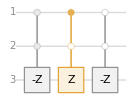

```mathematica
phaseOracle["Diagram"]
```

We shall prepare the 3-qubit in the index register states. To compare with the above truth table, we will create the index register states 0 in the order 2^n-1 down to 0 :

```mathematica
states=Table[QuantumState[{"Register",3,i}],{i,2^3-1,0,-1}];
```

Create a list with elements {|x>,(-1)^(f(x))|x>}:

```mathematica
TableForm[Transpose[{Table[QuantumState[{"Register",3,i}]["Formula"],{i,2^3-1,0,-1}],phaseOracle[#]["Formula"]&/@states}],TableHeadings->{None, {"|x>","(-1)^(f (x))|x>"}}]
```

|x> | (-1)^(f (x))|x>
111 | 111
110 | -110
101 | -101
100 | 100
011 | 011
010 | 010
001 | 001
000 | -000

As one can see, the oracle circuit reproduces the same result as the classical ones.

### Grover circuit with phase or Boolean oracles (3)

Let's define a Boolean function with only one solution (note in our framework, it does not matter if there is one or more solutions):

```mathematica
bf=And[q1,q2,q3];
```

Generate the corresponding Grover circuit using a phase oracle:

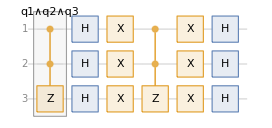

```mathematica
QuantumCircuitOperator[{"GroverPhase",bf}]["Diagram"]
```

Generate the corresponding Grover circuit using a Boolean oracle:

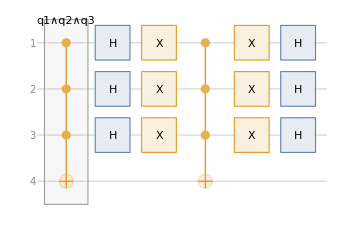

```mathematica
QuantumCircuitOperator[{"Grover",bf}]["Diagram"]
```

### The probability of success for the Grover algorithm (5)

Consider the following Boolean function and explore different cases and how the probability of success of the algorithm depends on circuit design or the initial state of the ancillary qubit:

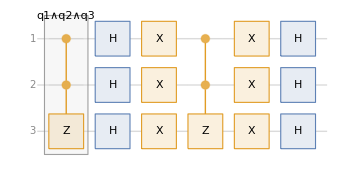

```mathematica
g=QuantumCircuitOperator[{"GroverPhase",bf}];
g["Diagram"]
```

Initial state for the circuit (qubit 1-6, each one in |x+>):

```mathematica
ψ0=QuantumState[{"UniformSuperposition",3}];
```

Apply the Grover operator 20 times:

```mathematica
steps=NestList[g,ψ0,20];
```

Calculate the success probability after each iteration:

```mathematica
success=QuantumState[{"Register",3,2^3-1}]["Dagger"][#]["Norm"]&/@steps;
```

Plot the success probability:

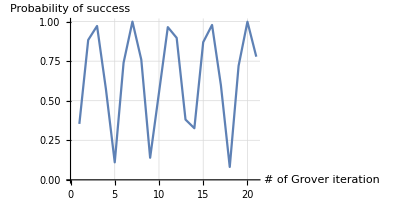

```mathematica
ListLinePlot[success,GridLines->Automatic,AxesLabel->{"# of Grover iteration","Probability of success" },AspectRatio->1/2]
```